```mathematica
Triangularprofit[{a_,z_}]:=(((-1+a) (2 2^(1/3) z+(-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)) (8 2^(1/3) z^3+2^(1/3) √3 √(z^4 (27 r^2-40 r z+16 z^2))-2 z^2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))+3 r z (-6 2^(2/3) (-1+a) z^2+2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)-3 (-1+a) z (-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))) (z^2-(4 z^2 (5 (-1+a) (2 2^(1/3) z+(-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)) (8 2^(1/3) z^3+2^(1/3) √3 √(z^4 (27 r^2-40 r z+16 z^2))-2 z^2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))+3 r z (-30 2^(2/3) (-1+a) z^2+4 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)-15 (-1+a) z (-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))) ((-1+a) (2 2^(1/3) z+(-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)) (8 2^(1/3) z^3+2^(1/3) √3 √(z^4 (27 r^2-40 r z+16 z^2))-2 z^2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))-3 r z (6 2^(2/3) (-1+a) z^2+4 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)+3 (-1+a) z (-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))))/((-1+a)^2 (-4 2^(1/3) z^2+2 z (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)+(-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3))^4)))/(18 z^3 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3))
```

```mathematica
parameters1={{1.251,1},{1.25,10},{1.25,15},{1.25,25},{1.25,30}};
```

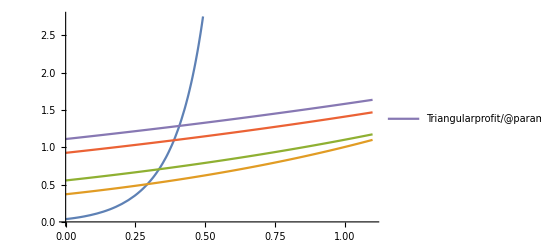

```mathematica
Plot[Triangularprofit/@parameters1,{r,0,1.1},Evaluated->True,PlotLegends->"AllExpressions"]
```

```mathematica
Plot[{(((-1+a) (2 2^(1/3) z+(-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)) (8 2^(1/3) z^3+2^(1/3) √3 √(z^4 (27 r^2-40 r z+16 z^2))-2 z^2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))+3 r z (-6 2^(2/3) (-1+a) z^2+2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)-3 (-1+a) z (-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))) (z^2-(4 z^2 (5 (-1+a) (2 2^(1/3) z+(-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)) (8 2^(1/3) z^3+2^(1/3) √3 √(z^4 (27 r^2-40 r z+16 z^2))-2 z^2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))+3 r z (-30 2^(2/3) (-1+a) z^2+4 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)-15 (-1+a) z (-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))) ((-1+a) (2 2^(1/3) z+(-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)) (8 2^(1/3) z^3+2^(1/3) √3 √(z^4 (27 r^2-40 r z+16 z^2))-2 z^2 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))-3 r z (6 2^(2/3) (-1+a) z^2+4 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)+3 (-1+a) z (-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3))))/((-1+a)^2 (-4 2^(1/3) z^2+2 z (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(1/3)+(-54 r z^2+40 z^3+6 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3))^4)))/(18 z^3 (-27 r z^2+20 z^3+3 √3 √(z^4 (27 r^2-40 r z+16 z^2)))^(2/3)),1/(2 (4+√(1-r)+4 3 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 3^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 3^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 3 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 5 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 5^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 5^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 5 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 9 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 9^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 9^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 9 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))},{r,0,1.1},Evaluated->True,PlotLegends->{"a=1.25","a=3","a=5","a=9"} ,AxesLabel->{"Product Degradation","Welfare"}]
```